# Function Definition

## Fermi Integral Function

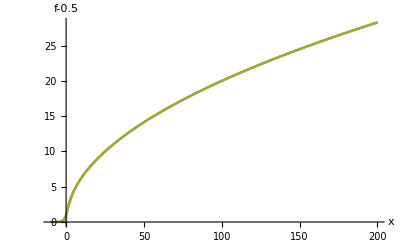

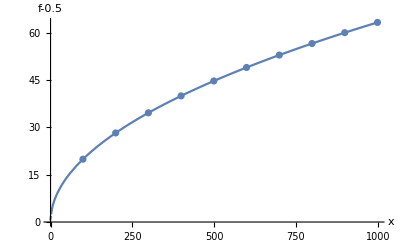

```mathematica
fermiintegral[j_,ζ_]:=-Gamma[1+j] PolyLog[1+j,-Exp[ζ]]
fermiintegralappro[j_,ζ_]:=1/(j+1) ζ^(j+1)
fermiintegralaymerich[j_,ξ_]:=(((j+1) 2^(j+1))/(b+ξ+(Abs[ξ-b]^c+a^c)^(1/c))^(j+1)+Exp[-ξ]/Gamma[j+1])^-1/.a->(1+15/4 (j+1)+1/40 (j+1)^2)^(1/2)/.b->1.8+0.61 j/.c->2+(2-Sqrt[2]) 2^-j
Plot[{fermiintegral[-0.5,x],fermiintegralappro[-.5,x],fermiintegralaymerich[-.5,x]},{x,-10,200},AxesLabel->{x,f-.5}]
Show[ListPlot[Table[{x,fermiintegralappro[-.5,x]},{x,-1,1000,100}]],Plot[fermiintegralaymerich[-.5,x],{x,-1,1000}],AxesLabel->{x,f-.5}]
```

```mathematica
TraditionalForm[(((j+1) 2^(j+1))/(b+ξ+(Abs[ξ-b]^c+a^c)^(1/c))^(j+1)+Exp[-ξ]/Gamma[j+1])^-1/.a->(1+15/4 (j+1)+1/40 (j+1)^2)^(1/2)/.b->1.8+0.61 j/.c->2+(2-Sqrt[2]) 2^-j];
```

## Unknown Parameters--lowest subband ΔUG

### Numerical calculation

#### Long Channel

```mathematica
numugamyrich[vgs_,vds_,r_,tox_,st_]:=Re[FindRoot[4 Pi ϵsi U==e/(Pi hbar) Sqrt[(kB T mt)/2] st[[1,1]] (fermiintegralaymerich[-0.5,(vgs-wgc+wfb-(4 Pi ϵsi U)/Cox[r,tox])/vt-Eq01]+fermiintegralaymerich[-0.5,(vgs-wgc+wfb-(4 Pi ϵsi U)/Cox[r,tox])/vt-Eq01-vds/vt]) /.Eq01->st[[1,4]]+st[[1,5]] U/vt,{U,0.01}][[1,2]]]
```

#### Short Channel

```mathematica
s[z_]:=Exp[-λ1/R[[n]] z]+(1-Exp[-λ1/R L]) Sinh[λ1/R z]/Sinh[λ1/R[[n]] L]
```

### Analytical Calculation

#### Long Channel

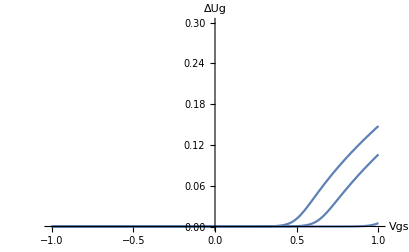

```mathematica
(*U[vgs_] := 
 b/(2 a) (-1 + Sqrt[1 + (4 a)/(b b) 1/25 Log[1 + Exp[25 (vgs + c)]]]) /. 
    a -> (8 Pi^4 hbar^2 ϵsi^2)/(subbandtable[[1, 1]]^2 e^3 mt) /. 
   b -> subbandtable[[1, 5]] + (4 Pi ϵsi)/Cox[2 nm, Tox] /. 
  c -> -wgc + wfb - besselenergylevel[0,1,mr,2 nm]/e*)
n={1,2,3};(*Radius Component*)
U[vgs_,n_] := 
 b/(2 a) (-1 + Sqrt[1 + (4 a)/(b b) 1/25 Log[1 + Exp[25 (vgs + c)]]]) /. 
    a -> (8 Pi^4 hbar^2 ϵsi^2)/(subbandtable[[1, 1]]^2 e^3 mt) /. 
   b -> subbandtable[[1, 5]] + (4 Pi ϵsi)/Cox[R, Tox][[n]] /. 
  c -> -wgc + wfb - subbandtable[[1, 3,n]]
Show[Plot[U[vgs,#]&/@n, {vgs, -1, 1},PlotRange->{{-1,1},{0,0.3}},AxesLabel->{Vgs,ΔUg}],Plot[U[vgs],{vgs,0,1}]]
```

```mathematica
Table[{vgs,U[vgs,3]},{vgs,0,1,.1}]
```

{{0.,6.28342×10^-8},{0.1,7.6546×10^-7},{0.2,9.32278×10^-6},{0.3,0.000113215},{0.4,0.0013285},{0.5,0.011515},{0.6,0.0402564},{0.7,0.0719018},{0.8,0.0999743},{0.9,0.125023},{1.,0.147819}}

#### Short Channel

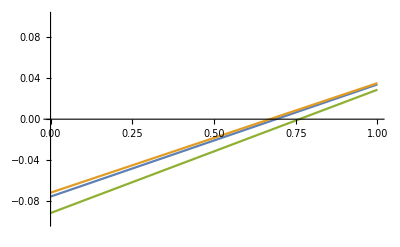

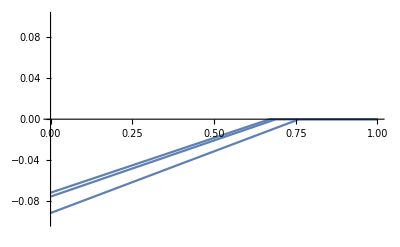

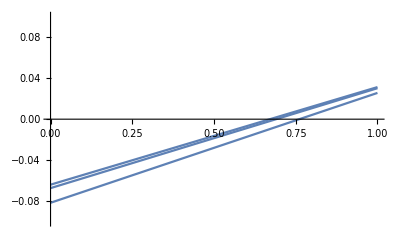

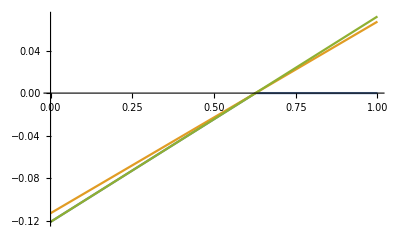

```mathematica
m={1,2,3};(*Channel Length Component*)
aug[vbi_,vgs_,vds_,z_,n_,m_]:=-(vbi-vgs+wgc-wfb) (Sinh[γ[[n]] (L[[m]]-z)]+Sinh[γ[[n]] z])/(Sinh[γ[[n]] L[[m]]] ((4 π ϵsi)/Cox[R[[n]],Tox]+1))-vds Sinh[γ[[n]] z]/(Sinh[γ[[n]] L[[m]]] ((4 π ϵsi)/Cox[R[[n]],Tox]+1))
augz[vbi_,vgs_,vds_,z_,n_,m_]:=(A Exp[γ[[n]] z]+B Exp[-γ[[n]] z]) (-1/((4 π ϵsi)/Cox[R,Tox][[n]]+1 ))/.A->NN ((vbi-vgs+wgc-wfb)(1-Exp[-γ[[n]] L[[m]]])+vds)/(Exp[γ[[n]] L[[m]]]-Exp[-γ[[n]] L[[m]]])/.B->NN ((vbi-vgs+wgc-wfb)(Exp[γ[[n]] L[[m]]]-1)-vds)/(Exp[γ[[n]] L[[m]]]-Exp[-γ[[n]] L[[m]]])/.NN->1/((1-γ[[n]]^2 R[[n]]^2/4)^2+γ[[n]]^2 R[[n]]^2/4)
(*aug[vbi_,vgs_,vds_,z_,m_]:=-(vbi-vgs+wgc-wfb) (Sinh[γ (L[[m]]-z)]+Sinh[γ z])/(Sinh[γ L[[m]]] ((4 π ϵsi)/Cox[R[[2]],Tox]+1))-vds Sinh[γ z]/(Sinh[γ L[[m]]] ((4 π ϵsi)/Cox[R[[2]],Tox]+1))*)
Maug[vbi_,vgs_,vds_,z_,n_,m_]:=If[Re[aug[vbi,vgs,vds,z,n,m]]≤0,Re[aug[vbi,vgs,vds,z,n,m]],0]
Plot[{aug[VBI[[2]],vgs,VDS8,2 nm,2,2],aug[VBI[[2]],vgs,VDS6,2 nm,2,3],aug[VBI[[2]],vgs,VDS8,2 nm,2,1]},{vgs,0,1},PlotRange->{-.1,.1}]
Plot[{Maug[VBI[[2]],vgs,VDS8,2 nm,2,#]&/@m},{vgs,0,1},PlotRange->{-.1,.1}]
Plot[{augz[VBI[[2]],vgs,VDS8,2 nm,2,#]&/@m},{vgs,0,1},PlotRange->{-.1,.1}]
Plot[{Maug[VBI[[3]],vgs,VDS5,2 nm,3,1],augz[VBI[[3]],vgs,VDS5,2 nm,3,1],aug[VBI[[3]],vgs,VDS5,2 nm,3,1]},{vgs,0,1}]
```

```mathematica
Cox[R[[n]],Tox]
Cox[R,Tox][[n]]
```

{5.35106×10^-10,7.54189×10^-10,9.72319×10^-10}

{5.35106×10^-10,7.54189×10^-10,9.72319×10^-10}

### Boundary Conditional Coefficients Calculation at the Source and the Drain

```mathematica
ugzero[vbi_,vgs_,n_,m_]:=(vbi-vgs+wgc-wfb)/-(α/R[[n]]^2)/.α->((4 π ϵsi)/Cox[R[[n]],Tox]+1) R[[n]]^2
ugLg[vbi_,vgs_,vds_,n_,m_]:=(vbi-vgs+wgc-wfb+vds)/-(α/R[[n]]^2)/.α->((4 π ϵsi)/Cox[R[[n]],Tox]+1) R[[n]]^2
ug[vbi_,vgs_,vds_,z_,n_,m_]:=1/Sinh[γ[[n]] L[[m]]] (ugzero[vbi,vgs,n,m] Sinh[γ[[n]] (L[[m]]-z)]+ugLg[vbi,vgs,vds,n,m] Sinh[γ[[n]] z])
```

## Subband Energy Level--lowest subband

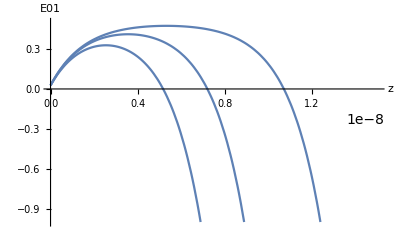

```mathematica
Eq01[vbi_,vgs_,vds_,z_,n_,m_]:=-e WS+kB T subbandtable[[1,4,n]]+subbandtable[[1,5]] e aug[vbi,vgs,vds,z,n,m]/.WS->vgs-wgc+wfb-(4 Pi ϵsi)/Cox[R[[n]],Tox] aug[vbi,vgs,vds,z,n,m]
Plot[{Eq01[VBI[[3]],VGS0,VDS8,z,3,#]&/@m/e},{z,0,15 nm},PlotRange->{-1,.5},AxesLabel->{z,E01}]
```

### Barrier Top

3.5678×10^-9

3.55553×10^-9

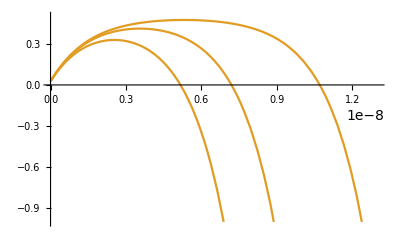

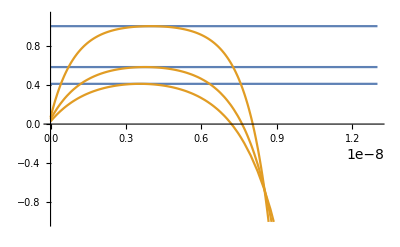

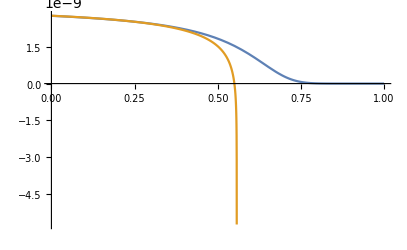

```mathematica
zmax[vbi_,vgs_,vds_,n_,m_]:=-1/(2 γ[[n]]) Log[B/A]/.A->ugzero[vbi,vgs,n,m]/(2 Sinh[γ[[n]] L[[m]]]) Exp[γ[[n]] L[[m]]]+ugLg[vbi,vgs,vds,n,m]/(2 Sinh[γ[[n]] L[[m]]])/.B->ugzero[vbi,vgs,n,m]/(2 Sinh[γ[[n]] L[[m]]]) Exp[-γ[[n]] L[[m]]]+ugLg[vbi,vgs,vds,n,m]/(2 Sinh[γ[[n]] L[[m]]])
zmaxz[vbi_,vgs_,vds_,n_,m_]:=1/(2 γ[[n]]) Log[B/A]/.A->NN ((vbi-vgs+wgc-wfb)(1-Exp[-γ[[n]] L[[m]]])+vds)/(Exp[γ[[n]] L[[m]]]-Exp[-γ[[n]] L[[m]]])/.B->NN ((vbi-vgs+wgc-wfb)(Exp[γ[[n]] L[[m]]]-1)-vds)/(Exp[γ[[n]] L[[m]]]-Exp[-γ[[n]] L[[m]]])/.NN->1/((1-γ[[n]]^2 R[[n]]^2/4)^2+γ[[n]]^2 R[[n]]^2/4)
zmax[VBI[[3]],VGS0,VDS8,3,2]
zmaxz[VBI[[3]],VGS0,VDS8,3,2]
Plot[{Eq01[VBI[[3]],VGS0,VDS8,zmax[VBI[[3]],VGS0,VDS8,3,#],2,#]&/@m/e,Eq01[VBI[[3]],VGS0,VDS8,z,3,#]&/@m/e},{z,0,13 nm},PlotRange->{-1,.5}]
Plot[{Eq01[VBI[[#]],VGS0,VDS8,zmax[VBI[[#]],VGS0,VDS8,#,2],#,2]&/@n/e,Eq01[VBI[[#]],VGS0,VDS8,z,#,2]&/@n/e},{z,0,13 nm},PlotRange->{-1,1.1}]
allzmax[vbi_,vgs_,vds_,n_,m_]:=1/(2 γ[[n]]) Log[1+1/b Log[1+Exp[b B/A]]]/.A->NN ((vbi-vgs+wgc-wfb)(1-Exp[-γ[[n]] L[[m]]])+vds)/(Exp[γ[[n]] L[[m]]]-Exp[-γ[[n]] L[[m]]])/.B->NN ((vbi-vgs+wgc-wfb)(Exp[γ[[n]] L[[m]]]-1)-vds)/(Exp[γ[[n]] L[[m]]]-Exp[-γ[[n]] L[[m]]])/.NN->1/((1-γ[[n]]^2 R[[n]]^2/4)^2+γ[[n]]^2 R[[n]]^2/4)/.b->0.1
Plot[{allzmax[VBI[[3]],vgs,.5,3,1],zmax[VBI[[3]],vgs,.5,3,1]},{vgs,0,1}]
```

```mathematica
Eq01[VBI[[#]],VGS0,VDS8,zmax[VBI[[#]],VGS0,VDS8,#,2],#,2]&/@n/e
```

{1.00083,0.582674,0.411222}

### Smoothing Function

```mathematica
DIBLSF[vgs_,n_]:=(1+Exp[μ ((e (vgs-wgc+wfb))/(kB T)-subbandtable[[1,4,n]]-ν)])^-1/.μ->0.6/.ν->-3
```

### All Region

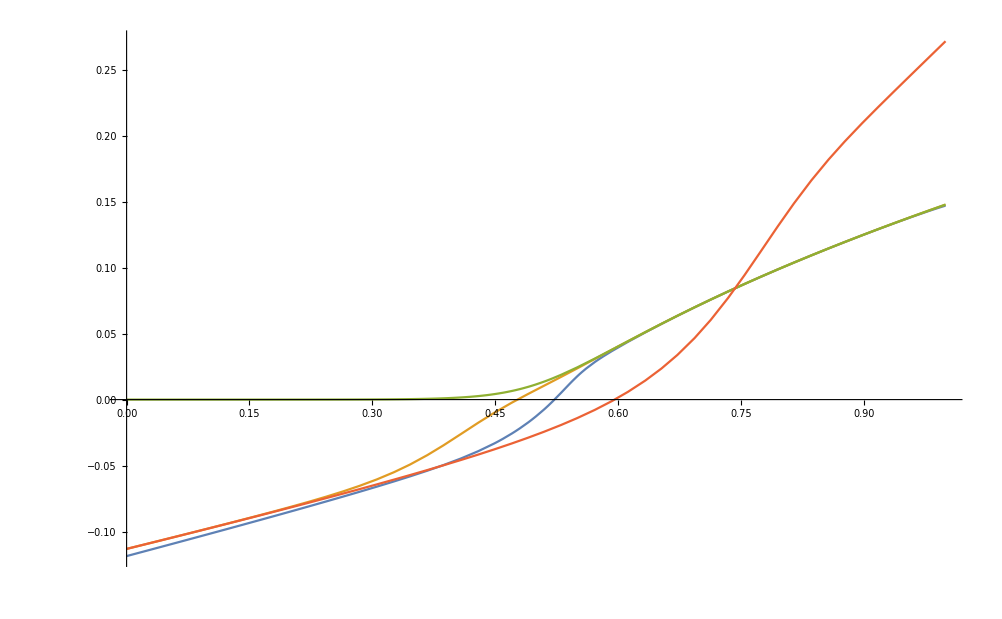

{{0.,-0.108252},{0.1,-0.093003},{0.2,-0.0770945},{0.3,-0.0581791},{0.4,-0.0273448},{0.5,0.00779185},{0.6,0.0402564},{0.7,0.0719018},{0.8,0.0999743},{0.9,0.125023},{1.,0.147819}}

{{0.,6.28342×10^-8},{0.1,7.6546×10^-7},{0.2,9.32278×10^-6},{0.3,0.000113215},{0.4,0.0013285},{0.5,0.011515},{0.6,0.0402564},{0.7,0.0719018},{0.8,0.0999743},{0.9,0.125023},{1.,0.147819}}

```mathematica
DIBLUG[vbi_,vgs_,vds_,n_,m_]:=Re[DIBLSF[vgs,n] Maug[vbi,vgs,vds,allzmax[vbi,vgs,vds,n,m],n,m]]+U[vgs,n]
allregnug[vgs_,vds_,r_,l_]:=Re[-(1/((1-γ[[r]]^2 R[[r]]^2/4)^2+γ[[r]]^2 R[[r]]^2/4)) 1/(Exp[γ[[r]] L[[l]]]-Exp[-γ[[r]] L[[l]]]) Sqrt[1/3Log[1+Exp[3 ((VBI[[r]]-vgs+wgc-wfb) (1-Exp[-γ[[r]] L[[l]]])+vds) ((VBI[[r]]-vgs+wgc-wfb) (Exp[γ[[r]] L[[l]]]-1)-vds)]]]]+U[vgs,r]
Plot[{allregnug[vgs,.5,3,1],DIBLUG[VBI[[3]],vgs,VDS6,3,1],U[vgs,3],aug[VBI[[3]],vgs,VDS6,allzmax[VBI[[3]],vgs,VDS6,3,1],3,1]},{vgs,0,1}(*,PlotRange->{{0.4,0.6},{-0.15,0.15}}*)]
Table[{vgs,DIBLUG[VBI[[3]],vgs,.5,3,1]},{vgs,0,1,.1}]
Table[{vgs,U[vgs,3]},{vgs,0,1,.1}]
```

### Parabolic Potential

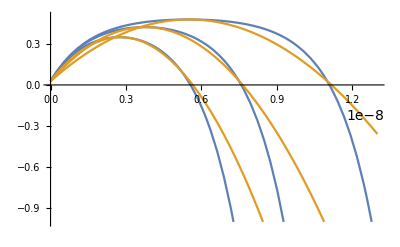

```mathematica
ParabEq01[vbi_,vgs_,vds_,z_,n_,m_]:=-a (z-zmax[VBI[[n]],vgs,vds,n,m])^2+c/.a->(Eq01[VBI[[n]],vgs,vds,zmax[VBI[[n]],vgs,vds,n,m],n,m]-Eq01[VBI[[n]],vgs,vds,0,n,m])/allzmax[VBI[[n]],vgs,vds,n,m]^2/.c->Eq01[VBI[[n]],vgs,vds,allzmax[VBI[[n]],vgs,vds,n,m],n,m]
Plot[{Eq01[VBI[[3]],VGS0,VDS5,z,3,#]&/@m/e,ParabEq01[VBI[[3]],VGS0,VDS5,z,3,#]&/@m/e},{z,0,13 nm},PlotRange->{-1,.5}]
```

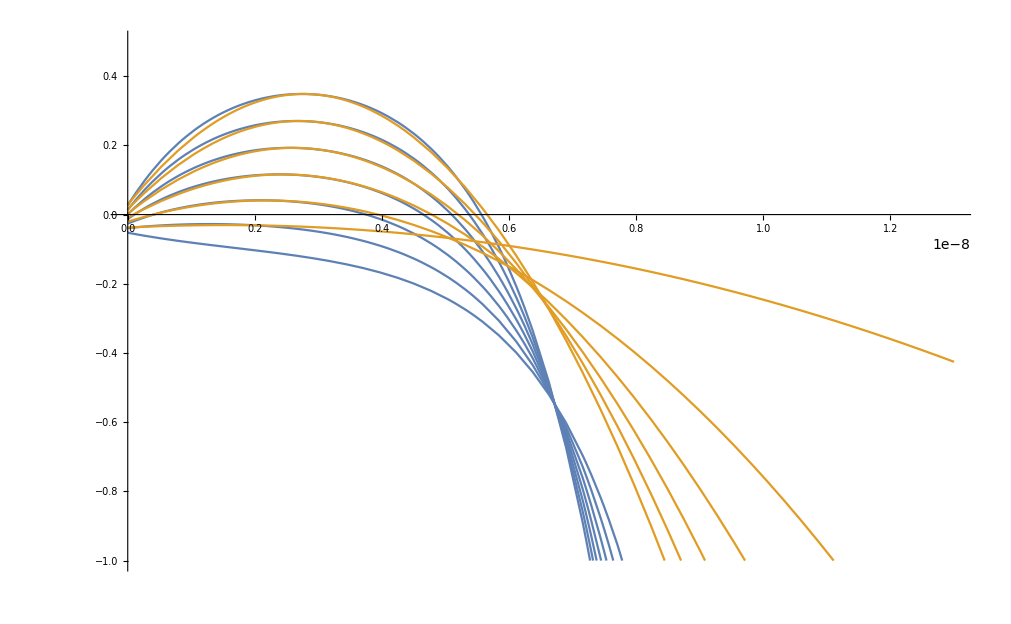

```mathematica
Plot[{Eq01[VBI[[3]],#,VDS5,z,3,1]&/@{0,.1,.2,.3,.4,.5,.6}/e,ParabEq01[VBI[[3]],#,VDS5,z,3,1]&/@{0,.1,.2,.3,.4,.5,.6}/e},{z,0,13 nm},PlotRange->{-1,.5}]
```

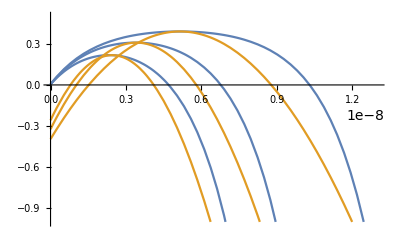

```mathematica
ParabEq02[vbi_,vgs_,vds_,z_,n_,m_]:=a (z-zmax[VBI[[n]],vgs,vds,n,m])^2+c/.a->-4 (γ[[n]])^2 e (subbandtable[[1,5]]+(4 Pi ϵsi)/Cox[R[[n]],Tox]) ((A^(1/2)-B^(1/2))/Log[B/A])^2/.A->NN ((vbi-vgs+wgc-wfb)(1-Exp[-γ[[n]] L[[m]]])+vds)/(Exp[γ[[n]] L[[m]]]-Exp[-γ[[n]] L[[m]]])/.B->NN ((vbi-vgs+wgc-wfb)(Exp[γ[[n]] L[[m]]]-1)-vds)/(Exp[γ[[n]] L[[m]]]-Exp[-γ[[n]] L[[m]]])/.NN->1/((1-γ[[n]]^2 R[[n]]^2/4)^2+γ[[n]]^2 R[[n]]^2/4)/.c->Eq01[VBI[[n]],vgs,vds,zmax[VBI[[n]],vgs,vds,n,m],n,m]
Plot[{Eq01[VBI[[4]],VGS0,VDS8,z,4,#]&/@m/e,ParabEq02[VBI[[4]],VGS0,VDS8,z,4,#]&/@m/e},{z,0,13 nm},PlotRange->{-1,.5}]
```

```mathematica
(Eq01[VBI[[4]],VGS0,VDS8,zmax[VBI[[4]],VGS0,VDS8,4,2],4,2]-Eq01[VBI[[4]],VGS0,VDS8,0,4,2])/zmax[VBI[[4]],VGS0,VDS8,4,2]^2
```

0.00418879

```mathematica
e (subbandtable[[1,5]]-(4 Pi ϵsi)/Cox[R[[4]],Tox]) (A^(1/2)-B^(1/2))^2/zmax[VBI[[4]],VGS0,VDS8,4,2]^2/.A->ugzero[VBI[[4]],VGS0,4,2]/(2 Sinh[γ[[4]] L[[2]]]) Exp[γ[[4]] L[[2]]]+ugLg[VBI[[4]],VGS0,VDS8,4,2]/(2 Sinh[γ[[4]] L[[2]]])/.B->ugzero[VBI[[4]],VGS0,4,2]/(2 Sinh[γ[[4]] L[[2]]]) Exp[-γ[[4]] L[[2]]]+ugLg[VBI[[4]],VGS0,VDS8,4,2]/(2 Sinh[γ[[4]] L[[2]]])
```

-0.00086906+0. ⅈ

```mathematica
Eq01[VBI[[4]],VGS0,VDS8,zmax[VBI[[4]],VGS0,VDS8,4,2],4,2]-Eq01[VBI[[4]],VGS0,VDS8,0,4,2]
 e (subbandtable[[1,5]]-(4 Pi ϵsi)/Cox[R[[4]],Tox]) (A^(1/2)-B^(1/2))^2/.A->NN ((VBI[[4]]-VGS0+wgc-wfb)(1-Exp[-γ[[4]] L[[2]]])+VDS8)/(Exp[γ[[4]] L[[2]]]-Exp[-γ[[4]] L[[2]]])/.B->NN ((VBI[[4]]-VGS0+wgc-wfb)(Exp[γ[[4]] L[[2]]]-1)-VDS8)/(Exp[γ[[4]] L[[2]]]-Exp[-γ[[4]] L[[2]]])/.NN->1/((1-γ[[4]]^2 R[[4]]^2/4)^2+γ[[4]]^2 R[[4]]^2/4)
```

4.87887×10^-20

1.94761×10^-20

```mathematica
A Exp[γ[[4]] zmax[VBI[[4]],VGS0,VDS8,4,2]]/.A->NN ((VBI[[4]]-VGS0+wgc-wfb)(1-Exp[-γ[[4]] L[[2]]])+VDS8)/(Exp[γ[[4]] L[[2]]]-Exp[-γ[[4]] L[[2]]])/.NN->1/((1-γ[[4]]^2 R[[4]]^2/4)^2+γ[[4]]^2 R[[4]]^2/4)
B Exp[-γ[[4]] zmax[VBI[[4]],VGS0,VDS8,4,2]]/.B->NN ((VBI[[4]]-VGS0+wgc-wfb)(Exp[γ[[4]] L[[2]]]-1)-VDS8)/(Exp[γ[[4]] L[[2]]]-Exp[-γ[[4]] L[[2]]])/.NN->1/((1-γ[[4]]^2 R[[4]]^2/4)^2+γ[[4]]^2 R[[4]]^2/4)
```

0.105106

0.100975

```mathematica
(A B)^{1/2}/.A->NN ((VBI[[4]]-VGS0+wgc-wfb)(1-Exp[-γ[[4]] L[[2]]])+VDS8)/(Exp[γ[[4]] L[[2]]]-Exp[-γ[[4]] L[[2]]])/.B->NN ((VBI[[4]]-VGS0+wgc-wfb)(Exp[γ[[4]] L[[2]]]-1)-VDS8)/(Exp[γ[[4]] L[[2]]]-Exp[-γ[[4]] L[[2]]])/.NN->1/((1-γ[[4]]^2 R[[4]]^2/4)^2+γ[[4]]^2 R[[4]]^2/4)
```

{0.103019}

```mathematica
Expand[(A^{1/2}-B^{1/2})^2]
```

{A-2 √A √B+B}

```mathematica
Table[{vgs,Re[Eq01[VBI[[3]],vgs,.5,zmax[VBI[[3]],vgs,.5,3,2],3,2]]/e},{vgs,0,1,.1}]
```

{{0.,0.422141},{0.1,0.333628},{0.2,0.245369},{0.3,0.157553},{0.4,0.0706614},{0.5,-0.0133602},{0.6,-0.0957315},{0.7,-0.195732},{0.8,-0.295732},{0.9,-0.395732},{1.,-0.495732}}

## WKB Approximation

### Turning Point

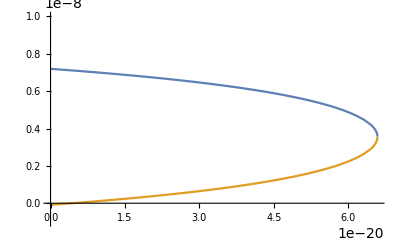

```mathematica
z01[vgs_,vds_,Ez_,n_,m_]:=Re[1/γ[[n]] Log[C01]/.C01->(-(b3-Ez)-Sqrt[(b3-Ez)^2-4 b1 b2])/(2 b1)/.b1->a1+a2/.b2->a1-a2/.b3->E01VGS/.a1->η01/2 ugzero[VBI[[n]],vgs,n,m]/.a2->-(η01/2) ugzero[VBI[[n]],vgs,n,m]/Sinh[γ[[n]] L[[m]]] (Cosh[γ[[n]] L[[m]]]-ugLg[VBI[[n]],vgs,vds,n,m]/ugzero[VBI[[n]],vgs,n,m])/.η01->(subbandtable[[1,5]]+(4 π ϵsi)/Cox[R[[n]],Tox]) e/.E01VGS->-e WS+kB T subbandtable[[1,4,n]]/.WS->vgs-wgc+wfb]
z02[vgs_,vds_,Ez_,n_,m_]:=Re[1/γ[[n]] Log[C02]/.C02->(-(b3-Ez)+Sqrt[(b3-Ez)^2-4 b1 b2])/(2 b1)/.b1->a1+a2/.b2->a1-a2/.b3->E01VGS/.a1->η01/2 ugzero[VBI[[n]],vgs,n,m]/.a2->-(η01/2) ugzero[VBI[[n]],vgs,n,m]/Sinh[γ[[n]] L[[m]]] (Cosh[γ[[n]] L[[m]]]-ugLg[VBI[[n]],vgs,vds,n,m]/ugzero[VBI[[n]],vgs,n,m])/.η01->(subbandtable[[1,5]]+(4 π ϵsi)/Cox[R[[n]],Tox]) e/.E01VGS->-e WS+kB T subbandtable[[1,4,n]]/.WS->vgs-wgc+wfb]
Plot[{z01[VGS0,VDS8,Ez,3,2],z02[VGS0,VDS8,Ez,3,2]},{Ez,0,Eq01[VBI[[3]],VGS0,VDS8,zmax[VBI[[3]],VGS0,VDS8,3,2],3,2]},PlotRange->{-10^-9,10^-8}]
```

### Transmission Coefficients

#### Numerical Calculation

```mathematica
V[vgs_,vds_,z_,Ez_,n_,m_]:=Eq01[VBI[[n]],vgs,vds,z,n,m]-Eq01[VBI[[n]],vgs,vds,0,n,m]-Ez
TF[vgs_,vds_,Ez_,n_,m_]:=Re[NIntegrate[Sqrt[V[vgs,vds,z,Ez,n,m]],{z,z02[vgs,vds,Ez,n,m],z01[vgs,vds,Ez,n,m]}]]
Numertranscoe[vgs_,vds_,Ez_,n_,m_]:=Exp[-2 Sqrt[(2 mt)/hbar^2] TF[vgs,vds,Ez,n,m]]
```

#### Parabolic Approximation

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {1.04926×10^-12}. NIntegrate obtained 1.44919×10^-18+7.35336×10^-21 ⅈ and 9.20734×10^-24 for the integral and error estimates.

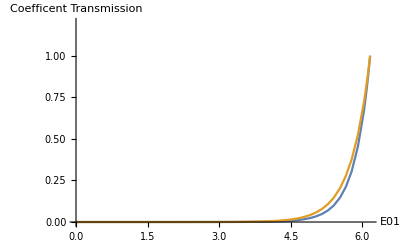

```mathematica
FlatVoltage [n_,m_]:= 
 FindRoot[Eq01[VBI[[n]], vgs, VDS8, 0,n,m] ==Eq01[VBI[[n]], vgs, VDS8, zmax[VBI[[n]], vgs, VDS8,n,m],n,m], {vgs, 0}][[1, 2]]
parabolictranscoe[vgs_,vds_,Ez_,n_,m_]:=If[vgs < FlatVoltage[n,m],Re[Exp[-π/hbar Sqrt[(2 mt)/a] (Eq01[VBI[[n]],vgs,vds,zmax[VBI[[n]],vgs,vds,n,m],n,m]-Ez-Eq01[VBI[[n]],vgs,vds,0,n,m])]]/.a->(Eq01[VBI[[n]],vgs,vds,zmax[VBI[[n]],vgs,vds,n,m],n,m]-Eq01[VBI[[n]],vgs,vds,0,n,m])/zmax[VBI[[n]],vgs,vds,n,m]^2,1]
Plot[{Numertranscoe[VGS0,VDS8,Ez,3,2],parabolictranscoe[VGS0,VDS8,Ez,3,2]},{Ez,0,Eq01[VBI[[3]],VGS0,VDS8,zmax[VBI[[3]],VGS0,VDS8,3,2],3,2]-Eq01[VBI[[3]],VGS0,VDS8,0,3,2]},PlotRange->{0,1.2},AxesLabel->{E01,Transmission Coefficent}]
FlatVoltage[3,2];
```

```mathematica
allunitranscoe[vgs_,Ez_,n_,m_]:=Re[(Exp[1/a Log[1+Exp[(a Pi)/hbar Sqrt[(2 mt)/(Eq01[VBI[[n]],vgs,0.5,zmax[VBI[[n]],vgs,0.5,n,m],n,m]-Eq01[VBI[[n]],0,0.5,0,n,m])] allzmax[VBI[[n]],vgs,0.5,n,m] ((Eq01[VBI[[n]],vgs,0.5,allzmax[VBI[[n]],vgs,0.5,n,m],n,m]-Eq01[VBI[[n]],vgs,0.5,0,n,m])-Ez)]]])^(-1)/. a->10]
```

```mathematica
Plot[allunitranscoe[0.4,Ez,3,1],{Ez,-e,e}]
```

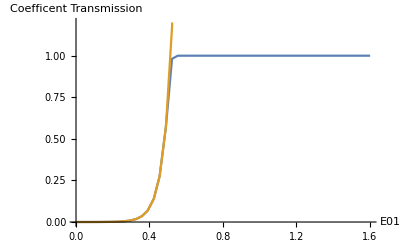

```mathematica
Plot[{allunitranscoe[0,Ez,3,1],parabolictranscoe[VGS0,VDS5,Ez,3,1]},{Ez,0,e},PlotRange->{0,1.2},AxesLabel->{E01,Transmission Coefficent},PlotRange->{All,{0,1.1}}]
```

## Current Function--lowest subband

### Numerical calculation

#### Long Channel

```mathematica
numids[vgs_,vds_,r_,tox_,st_]:=  (e kB T)/(Pi hbar) st[[1,1]] (Log[1+Exp[1/vt(vgs-wgc+wfb-(4 Pi ϵsi numugamyrich[vgs,vds,r,tox,st])/Cox[r,tox])-st[[1,4]]-st[[1,5]]/vt numugamyrich[vgs,vds,r,tox,st]]]-Log[1+Exp[1/vt(vgs-wgc+wfb-(4 Pi ϵsi numugamyrich[vgs,vds,r,tox,st])/Cox[r,tox])-st[[1,4]]-st[[1,5]]/vt numugamyrich[vgs,vds,r,tox,st]-vds/vt]])
```

#### Short Channel

### Analytical calculation

#### Long Channel

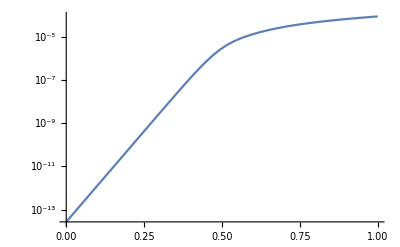

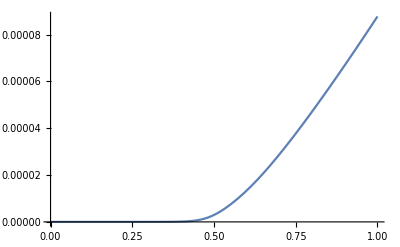

```mathematica
anaids[vgs_,vds_,st_,n_]:=  (e kB T)/(Pi hbar) st[[1,1]] (Log[1+Exp[1/vt(vgs-wgc+wfb-(4 Pi ϵsi U[vgs,n])/Cox[R[[n]],Tox])-st[[1,4,n]]-st[[1,5]]/vt U[vgs,n]]]-Log[1+Exp[1/vt(vgs-wgc+wfb-(4 Pi ϵsi U[vgs,n])/Cox[R[[n]],Tox])-st[[1,4,n]]-st[[1,5]]/vt U[vgs,n]-vds/vt]])
LogPlot[anaids[vgs,VDS6,subbandtable,3],{vgs,0,1}]
Plot[anaids[vgs,VDS6,subbandtable,3],{vgs,0,1}]
```

#### Short Channel

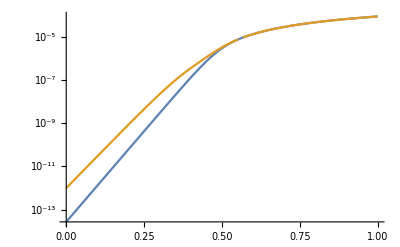

```mathematica
diblanaids[vbi_,vgs_,vds_,st_,n_,m_]:=Re[(e kB T)/(Pi hbar) st[[1,1]] (Log[1+Exp[1/vt (vgs-wgc+wfb-(4 Pi ϵsi DIBLUG[vbi,vgs,vds,n,m])/Cox[R[[n]],Tox])-st[[1,4,n]]-st[[1,5]]/vt DIBLUG[vbi,vgs,vds,n,m]]]-Log[1+Exp[1/vt (vgs-wgc+wfb-(4 Pi ϵsi DIBLUG[vbi,vgs,vds,n,m])/Cox[R[[n]],Tox])-st[[1,4,n]]-st[[1,5]]/vt DIBLUG[vbi,vgs,vds,n,m]-vds/vt]])]
(*LogPlot[diblanaids[VBI[[3]],vgs,VDS6,subbandtable,3,2],{vgs,0,1}]*)
LogPlot[{anaids[vgs,VDS8,subbandtable,3],diblanaids[VBI[[3]],vgs,VDS8,subbandtable,3,2]},{vgs,0,1}]
```

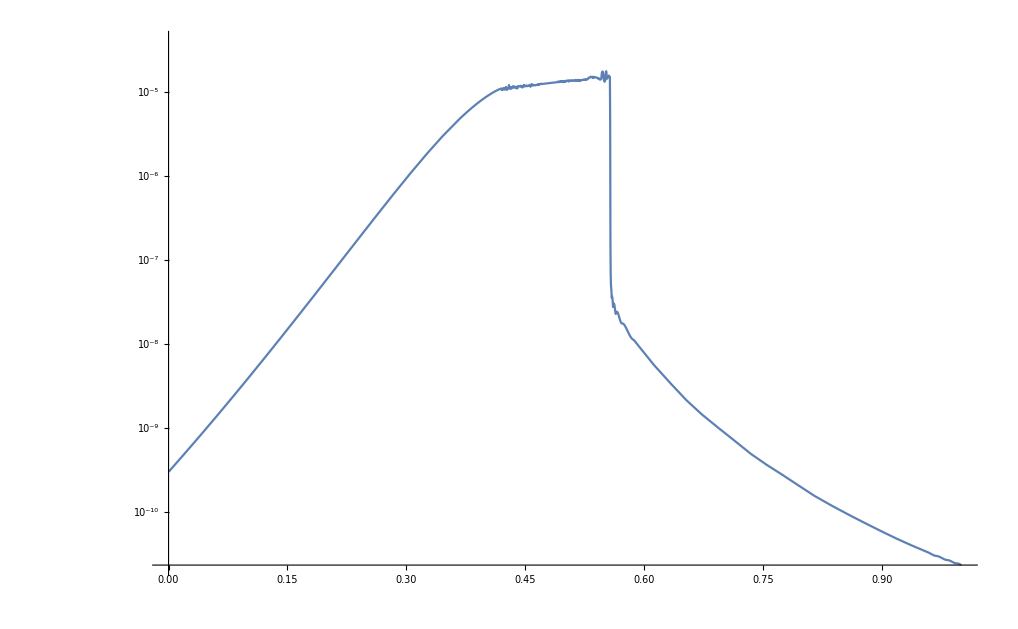

```mathematica
LogPlot[e/(Pi hbar)
subbandtable[[1,1]] NIntegrate[Re[allunitranscoe[vgs,Ez,3,1]/(1+Exp[(Eq01[VBI[[3]],vgs,0.5,0,3,1]+Ez)/(kB T)])],{Ez,0,10 e}],{vgs,0,1},PlotRange->{All,{0,.00004}}]
```

## Tunneling Current

### Numerical Calculation

```mathematica
numtunnelcurrent[vgs_,vds_,st_,n_,m_]:=If[vgs<FlatVoltage[n,m],Re[e/(π hbar) st[[1,1]] NIntegrate[Numertranscoe[vgs,vds,Ez,n,m]/(1+Exp[(Eq01[VBI[[n]],vgs,vds,0,n,m]+Ez)/(kB T)]),{Ez,0,-Eq01[VBI[[n]],vgs,vds,0,n,m]+Eq01[VBI[[n]],vgs,vds,zmax[VBI[[n]],vgs,vds,n,m],n,m]}]],0]
LogPlot[numtunnelcurrent[vgs,VDS8,subbandtable,2,2],{vgs,0,1}]
numtunnelcurrent[vgs_,vds_,st_]:=If[vgs<FlatVoltage[2,2],Re[e/(π hbar) st[[1,1]] 
NIntegrate[Numertranscoe[vgs,vds,Ez,2,2]/(1+Exp[(Eq01[VBI[[2]],vgs,vds,0,2,2]+Ez)/(kB T)]),{Ez,0,-Eq01[VBI[[2]],vgs,vds,0,2,2
]+Eq01[VBI[[2]],vgs,vds,zmax[VBI[[2]],vgs,vds],2,2]}]],0]
LogPlot[numtunnelcurrent[vgs,VDS8,subbandtable,4,2],{vgs,0,1}]
```

NIntegrate::nlim: z = 1.24166×10^-9 Re[Log[-2.25879×10^21 (-1.02506×10^-19+√(-8.37966×10^-41+Power[«2»])+Ez)]] is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

$Aborted

$Aborted

### Analytical Calculation

```mathematica
parabolicapproxtunnelcurrent[vgs_, vds_, st_,n_,m_] := 
 If[vgs < FlatVoltage[n,m], 
  Re[e/(π hbar) st[[1, 1]] NIntegrate[
     parabolictranscoe[vgs, vds, 
       Ez,n,m]/( Exp[(Eq01[VBI[[n]],vgs,vds, 0,n,m] + Ez)/(kB T)]), {Ez, 
      0, -Eq01[VBI[[n]], vgs, vds, 0,n,m] + 
       Eq01[VBI[[n]], vgs, vds, zmax[VBI[[n]],vgs,vds,n,m],n,m]}]], 0]
LogPlot[parabolicapproxtunnelcurrent[vgs,VDS8,subbandtable,3,2],{vgs,0,1}]
```

Part::partd: Part specification subbandtable⟦1,4,3⟧ is longer than depth of object.

Part::partd: Part specification γ⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

FindRoot::nlnum: The function value {1.79496×10^-20-5.31975×10^-20 subbandtable⟦1,5⟧-1.60218×10^-19 subbandtable⟦1,5⟧ (0.482957 Csch[8.5×10^-9 Part[«2»]] Sinh[0.5 Log[«1»]]-0.332033 Csch[8.5×10^-9 Part[«2»]] (-1. Sinh[«1»]+Sinh[Times[«2»]]))+1.60218×10^-19 (-0.33-0.656464 (0.482957 Csch[«1»] Sinh[«1»]-0.332033 Csch[«1»] Plus[«2»]))} is not a list of numbers with dimensions {1} at {vgs} = {0.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

-Graphics-

```mathematica
LogPlot[{numtunnelcurrent[vgs,VDS8,subbandtable,4,2],parabolicapproxtunnelcurrent[vgs,VDS8,subbandtable,4,2]},{vgs,0,1}]
```

Part::partd: Part specification subbandtable⟦1,4,4⟧ is longer than depth of object.

Part::partd: Part specification γ⟦4⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

FindRoot::nlnum: The function value {2.47358×10^-20-5.3575×10^-20 subbandtable⟦1,5⟧-1.60218×10^-19 subbandtable⟦1,5⟧ (0.524531 Csch[8.5×10^-9 Part[«2»]] Sinh[0.5 Log[«1»]]-0.334389 Csch[8.5×10^-9 Part[«2»]] (-1. Sinh[«1»]+Sinh[Times[«2»]]))+1.60218×10^-19 (-0.33-0.525171 (0.524531 Csch[«1»] Sinh[«1»]-0.334389 Csch[«1»] Plus[«2»]))} is not a list of numbers with dimensions {1} at {vgs} = {0.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

-Graphics-

### Smoothing Function

```mathematica
TotalSF[vgs_,n_]:=(1+Exp[μ ((e (vgs-wgc+wfb))/(kB T)-subbandtable[[1,4,n]]-ν)])^-1/.μ->0.7/.ν->-7
totalcurrent[vgs_,vds_,st_,n_,m_]:=parabolicapproxtunnelcurrent[vgs, vds, st,n,m] TotalSF[vgs,n]+diblanaids[VBI[[n]],vgs,vds,st,n,m]
LogPlot[totalcurrent[vgs,VDS8,subbandtable,3,2],{vgs,0,.6}]
Plot[totalcurrent[vgs,VDS8,subbandtable,3,2],{vgs,0,.8},PlotRange->All]
```

Part::partd: Part specification subbandtable⟦1,4,3⟧ is longer than depth of object.

Part::partd: Part specification γ⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

FindRoot::nlnum: The function value {1.79496×10^-20-5.31975×10^-20 subbandtable⟦1,5⟧-1.60218×10^-19 subbandtable⟦1,5⟧ (0.482957 Csch[8.5×10^-9 Part[«2»]] Sinh[0.5 Log[«1»]]-0.332033 Csch[8.5×10^-9 Part[«2»]] (-1. Sinh[«1»]+Sinh[Times[«2»]]))+1.60218×10^-19 (-0.33-0.656464 (0.482957 Csch[«1»] Sinh[«1»]-0.332033 Csch[«1»] Plus[«2»]))} is not a list of numbers with dimensions {1} at {vgs} = {0.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

-Graphics-

Part::partd: Part specification subbandtable⟦1,4,3⟧ is longer than depth of object.

Part::partd: Part specification γ⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

FindRoot::nlnum: The function value {1.79496×10^-20-5.31975×10^-20 subbandtable⟦1,5⟧-1.60218×10^-19 subbandtable⟦1,5⟧ (0.482957 Csch[8.5×10^-9 Part[«2»]] Sinh[0.5 Log[«1»]]-0.332033 Csch[8.5×10^-9 Part[«2»]] (-1. Sinh[«1»]+Sinh[Times[«2»]]))+1.60218×10^-19 (-0.33-0.656464 (0.482957 Csch[«1»] Sinh[«1»]-0.332033 Csch[«1»] Plus[«2»]))} is not a list of numbers with dimensions {1} at {vgs} = {0.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

-Graphics-